# Import data

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir="../"<>getCacheDirRaw[volExp,noIP3R];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

## Import transformation

```mathematica
cdir="../"<>getCacheDirRaw[volExp,noIP3R];

SetDirectory[NotebookDirectory[]];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{2118.58,6323.61},{1934.71,5726.05}}

## Import cache and transformations

```mathematica
SetDirectory[NotebookDirectory[]];

ip3s={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

params0=<|
"with_trans"->Association[],
"without_trans"->Association[]
|>;

cdir="../"<>getCacheDirRaw[volExp,noIP3R];
Monitor[
Do[
ip3=ip3s[[idx]];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0["with_trans"][ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]]

cdir=getCacheDirRaw[volExp,noIP3R];
Monitor[
Do[
ip3=ip3s[[idx]];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"params0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

params0["without_trans"][ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]]
```

```mathematica
pltEvery=10;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

# Import rxn graph

```mathematica
SetDirectory[NotebookDirectory[]];
graph=Import["../train/training_data/training_data_rxns/graph_inputs_wo_std.wlnet"];
```

# Jacobian

```mathematica
getJacNorm[graph_,tpt_,params0_,ip3_]:=Module[
{input,noOutputs,jac,jac0,output}
,
input=params0[ip3]["LD"][[tpt]];
input["tpt"]=tpt;

output=graph[input];

noOutputs=60;

jac={};
Do[

jac0={};
Do[

input[NetPortGradient["Output"]]=UnitVector[noOutputs,iNum];
AppendTo[jac0,graph[input,NetPortGradient[denom]]];
,{denom,{"wt","b","sig2"}}];
jac0=Flatten[jac0];

(*jac0/=output[[iNum]]+10^-6;*)

AppendTo[jac,jac0];
,{iNum,1,noOutputs}];

Return[jac]
]
```

```mathematica
tpt=50;
ip3="ip3_0p700";
jac=<|
"with_trans"->getJacNorm[graph,tpt,params0["with_trans"],ip3],
"without_trans"->getJacNorm[graph,tpt,params0["without_trans"],ip3]
|>;
```

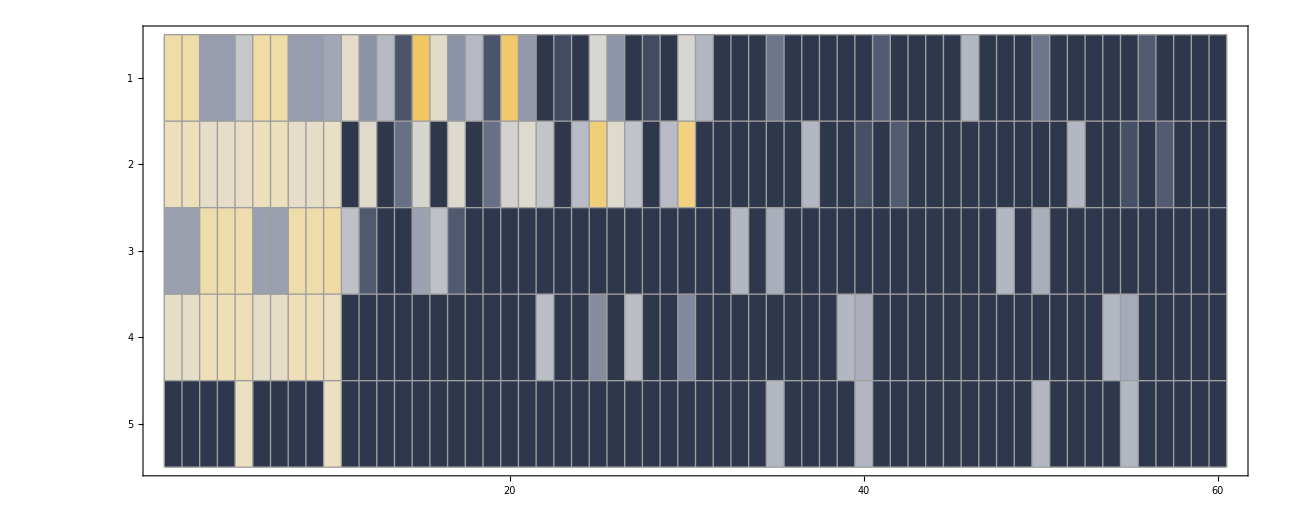

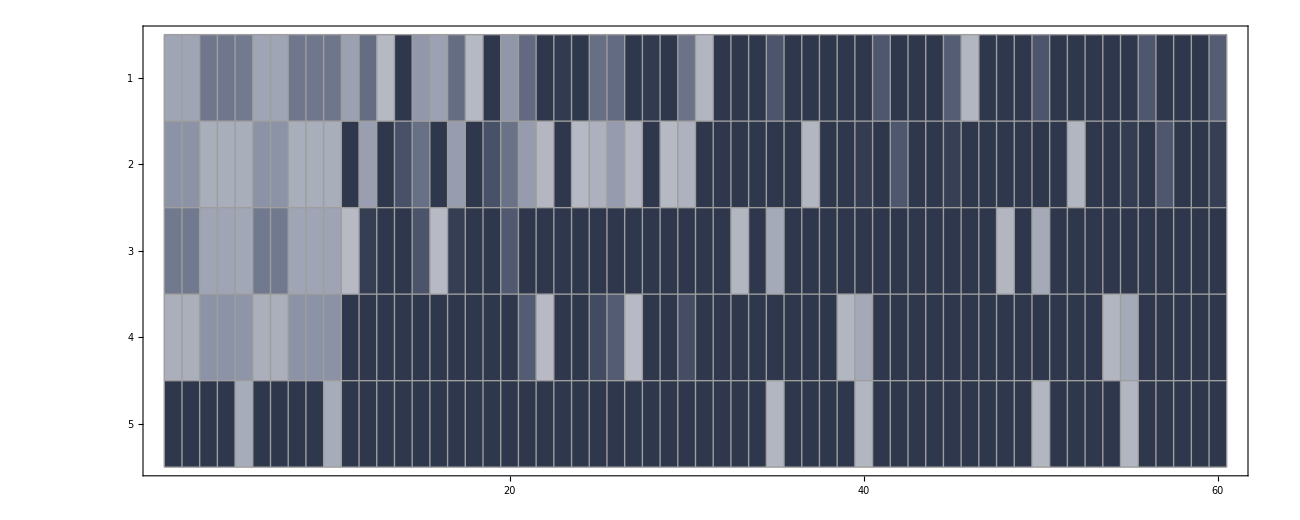

```mathematica
jacPlt=Abs[Transpose[jac["without_trans"]]];
jacPlt+=Exp[-30];
jacPlt=Log[jacPlt];
pWithout=MatrixPlot[jacPlt,ImageSize->1300,PlotRange->{-30,15},ColorFunction->"GrayYellowTones",Axes->None,Mesh->True]

jacPlt=Abs[Transpose[jac["with_trans"]]];
jacPlt+=Exp[-30];
jacPlt=Log[jacPlt];
pWith=MatrixPlot[jacPlt,ImageSize->1300,PlotRange->{-30,15},ColorFunction->"GrayYellowTones",Mesh->True]
```

```mathematica
leg=BarLegend[{"GrayYellowTones",{-30,15}},LabelStyle->Directive[FontSize->24]]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/leg.pdf",leg];
Export["figures/jac_with_trans.pdf",pWith];
Export["figures/jac_without_trans.pdf",pWithout];
```